```mathematica
RndExp[rate_]:=-Log[RandomReal[]]/rate//N;
```

```mathematica
mu=100;
landa=80;
nmuestras=1000;
```

```mathematica
Service=Table[RndExp[mu],nmuestras];
```

```mathematica
InterArrivals=Table[RndExp[landa],nmuestras];
```

----- Hacemos la función acumulativa -----

```mathematica
Acumulador[lst_]:=Module[{acum=0},Map[(acum+=#;acum)&,lst]];
```

## ----- Calculamos los valores acumulativos -----

```mathematica
Arrivals=Accumulate[InterArrivals];
```

----- Creamos la funcion que aplicara las propiedades de nuestra cola -----

```mathematica
Fifo[Arrivals_,Service_]:=Module[{n,checkTime},
n=0;
checkTime=Arrivals[[1]];
Map[(n++;If [checkTime>=#,checkTime+=Service[[n]],checkTime=#+Service[[n]]])&,Arrivals]
]
```

----- Aplicamos la funcion para obtener los tiempos de salida y representamos-----

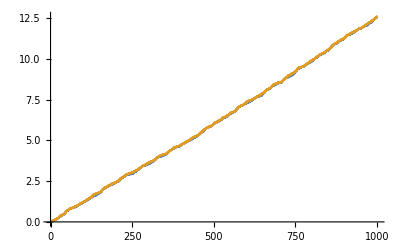

```mathematica
Departures=Fifo[Arrivals,Service];
ListStepPlot[{Arrivals,Departures}]
```

----- Prueba de FIFO usando n++ fuera de la función principal -----

```mathematica
b={1,2,3,4,5};
Module[{n},n=0;Map[(n++;b[[n]])&,b]]
```

{1,2,3,4,5}

--------------------------------------------------------------------------------------

```mathematica
numadd[lst_]:=Module[{num},num=0;Map[(num++;{#,num})&,lst]]
arr=numadd[Arrivals];
depa=numadd[Departures];
```

```mathematica
Manipulate[ListStepPlot[{arr[[ori;;ori+width]],depa[[ori;;ori+width]]}],{ori,1,nmuestras-width,10},{width,5,700,5}]
```

----- Haciendo las “montañas” (cantidad de paquetes por tiempo) -----

```mathematica
Mark[lst_,m_]:=Map[({#,m})&,lst]
```

```mathematica
ArrivalsMark=Mark[Arrivals,1];
DeparturesMark=Mark[Departures,-1];
```

```mathematica
EventMark=Sort[Join[ArrivalsMark,DeparturesMark]];(*Juntamos*)
```

```mathematica
Mont[EventMark_]:=Module[{cant},cant=0;Map[(If[#[[2]]==1,cant++,cant--];{#[[1]],cant})&,EventMark]]
```

```mathematica
MontList=Mont[EventMark];
```

```mathematica
Manipulate[ListStepPlot[MontList[[ori;;ori+width]]],{ori,1,nmuestras-width,10},{width,10,150,5}]
```